```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\flux_pmf\xin\PVP10\111Ag\1_IC_US\11ns\k_0.7\ui

```mathematica
log=OpenRead["fe_ui.xy"];
Find[log," # Reaction coordinate"];
pmfUI=ReadList[log,{Number,Number}];
Close[log];
```

```mathematica
T=433;
(*K*)
R=0.0019872041;
(*kcal/mol.K*)
kbJ=1.3806*10^-23;
(*J/K*)
```

```mathematica
betaR=1/(R*T)
```

1.16217

```mathematica
betaJ=1/(kbJ*T)
```

1.6728×10^20

```mathematica
dx=10^(-10)*(pmfUI[[3,1]]-pmfUI[[1,1]])/2
```

2.5×10^-12

```mathematica
mass=0.1078682/(6.022*10^23);
(*Atomic mass of Ag atom kg/mol*)
```

```mathematica
pmfUI0=pmfUI;
```

```mathematica
pmfUI0[[All,2]]=pmfUI[[All,2]]-pmfUI[[-500,2]];
```

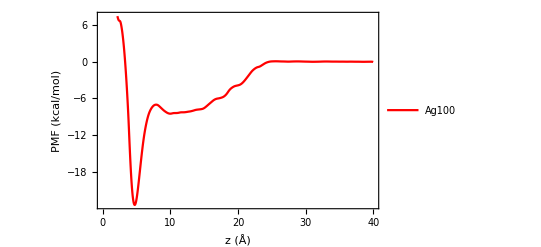

```mathematica
GraphPMF0=ListLinePlot[{pmfUI0[[85;;-400]]},FrameLabel->{Style["z (Å)",Bold],Style["PMF (kcal/mol)",Bold]},LabelStyle->{FontFamily->"Helvetica",Black},PlotStyle->{Red},PlotRange->{{0,40},All},PlotLegends->{"Ag100"},Frame->True,FrameStyle->Thickness[0.0025]]
```

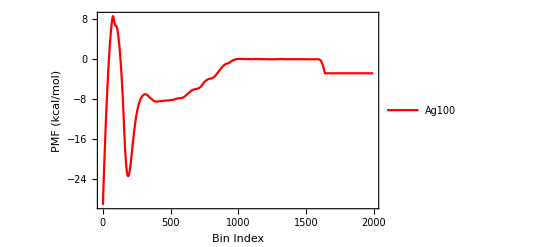

```mathematica
ListLinePlot[{pmfUI0[[All,2]]},FrameLabel->{Style["Bin Index",Bold],Style["PMF (kcal/mol)",Bold]},LabelStyle->{FontFamily->"Helvetica",Black},PlotStyle->{Red},PlotRange->All,PlotLegends->{"Ag100"},Frame->True,FrameStyle->Thickness[0.0025]]
```

```mathematica
MinPos=Position[pmfUI[[100;;-1,2]],Min[pmfUI[[100;;-1,2]]]][[1,1]]+100
```

188

```mathematica
TranPos=Position[pmfUI[[MinPos;;MinPos+200,2]],Max[pmfUI[[MinPos;;MinPos+200,2]]]][[1,1]]+MinPos
```

314

```mathematica
MinAPos=Position[pmfUI[[TranPos;;TranPos+200,2]],Min[pmfUI[[TranPos;;TranPos+200,2]]]][[1,1]]+TranPos
```

398

```mathematica
dA=R*T;
(*Basin definition*)
```

```mathematica
LeftMinAPos=Position[pmfUI[[MinAPos-100;;MinAPos,2]],Nearest[pmfUI[[MinAPos-100;;MinAPos,2]],pmfUI[[MinAPos,2]]+dA][[1]]][[1,1]]+MinAPos-100
```

347

```mathematica
RightMinAPos=Position[pmfUI[[MinAPos;;MinAPos+300,2]],Nearest[pmfUI[[MinAPos;;MinAPos+300,2]],pmfUI[[MinAPos,2]]+dA][[1]]][[1,1]]+MinAPos
```

596

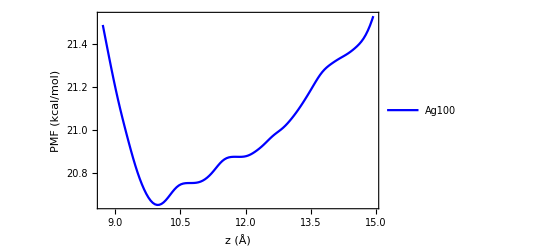

```mathematica
ListLinePlot[pmfUI[[LeftMinAPos;;RightMinAPos]],FrameLabel->{Style["z (Å)",Bold],Style["PMF (kcal/mol)",Bold]},LabelStyle->{FontFamily->"Helvetica",Black},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"Ag100"},Frame->True,FrameStyle->Thickness[0.0025]]
```

```mathematica
flux=0.5*(2/(Pi*betaJ*mass))^0.5*Exp[-pmfUI[[TranPos,2]]*betaR]/(Integrate[Interpolation[Exp[-pmfUI[[LeftMinAPos;;RightMinAPos,2]]*betaR]][x],{x,1,RightMinAPos-LeftMinAPos+1}]*dx)
```

3.0668×10^10

```mathematica
Export["flux.txt",flux];
```